## Flight-gate problem

Бронников Егор ПМ-1901

### Данные

```mathematica
numberOfFlights = 10;
numberOfGates=3;
maxTimeStart=100;
tmin=3;
landing:=RandomInteger[{5,10}]
tow:=RandomInteger[{3,5}]
parking:=RandomInteger[{5,15}]
```

```mathematica
Clear[getArrivalInterval]
getArrivalInterval[time_]:={time,time+landing}
```

```mathematica
Clear[getParkingInterval]
getParkingInterval[arr:{_,time_}]:={arr,{#,#+parking}&[time+tow]}
```

```mathematica
Clear[getDepartureInterval]
getDepartureInterval[{arr_,park:{_,time_}}]:={arr,park,{#,#+landing}&[time+tow]}
```

```mathematica
Composition[getDepartureInterval,getParkingInterval,getArrivalInterval][10](*1 список - arrival, 2 список - parking,
3 список - departure*)
```

{{10,17},{22,34},{38,47}}

```mathematica
timeIntervals=Table[
Composition[RandomChoice[{0.8,0.2}->{getDepartureInterval,Identity}],getParkingInterval,getArrivalInterval]@RandomInteger[{0,maxTimeStart}],
numberOfFlights
];
```

```mathematica
timeIntervals
```

{{{19,28},{33,48}},{{60,66},{70,78},{81,88}},{{49,58},{63,69},{73,79}},{{9,17},{21,31},{34,40}},{{49,59},{62,71}},{{7,13},{16,24},{29,36}},{{73,83},{86,96},{101,106}},{{47,57},{61,69},{72,77}},{{6,14},{18,32}},{{45,52},{55,70},{73,82}}}

```mathematica
maxTime=Max@timeIntervals;
```

```mathematica
events=TakeList[Range@Length@Flatten[#,1],Length/@#]&@timeIntervals;
```

```mathematica
events
```

{{1,2},{3,4,5},{6,7,8},{9,10,11},{12,13},{14,15,16},{17,18,19},{20,21,22},{23,24},{25,26,27}}

```mathematica
pf=RandomInteger[{1,20},numberOfGates]&/@Flatten[events];
```

```mathematica
pf
```

{{1,6,17},{2,6,3},{5,9,13},{1,8,16},{18,19,4},{15,20,7},{19,7,2},{12,14,18},{10,18,13},{18,7,14},{16,16,17},{18,12,4},{20,3,10},{3,17,14},{8,8,8},{16,10,19},{1,16,16},{3,13,18},{6,15,19},{10,4,6},{12,9,4},{18,13,11},{11,10,17},{4,9,7},{10,16,18},{18,14,15},{3,11,7}}

M(i) ∀ i ∈ N (допустимые гейты)

```mathematica
posPref=Flatten[RandomSample[#,RandomInteger[{0,Length@#-1}]]&/@MapIndexed[#2&,pf,{2}],1];
```

```mathematica
posPref
```

{{1,1},{2,3},{3,3},{3,1},{4,1},{4,2},{5,1},{6,3},{7,1},{8,1},{8,2},{9,3},{12,3},{12,2},{16,2},{17,1},{17,3},{18,3},{18,2},{19,2},{19,3},{20,1},{21,2},{21,3},{22,2},{22,1},{23,2},{23,1},{24,1},{24,2},{25,3},{27,1},{27,2}}

```mathematica
preferences=ReplacePart[pf,posPref->-∞];
```

```mathematica
preferences
```

{{-∞,6,17},{2,6,-∞},{-∞,9,-∞},{-∞,-∞,16},{-∞,19,4},{15,20,-∞},{-∞,7,2},{-∞,-∞,18},{10,18,-∞},{18,7,14},{16,16,17},{18,-∞,-∞},{20,3,10},{3,17,14},{8,8,8},{16,-∞,19},{-∞,16,-∞},{3,-∞,-∞},{6,-∞,-∞},{-∞,4,6},{12,-∞,-∞},{-∞,-∞,11},{-∞,-∞,17},{-∞,-∞,7},{10,16,-∞},{18,14,15},{-∞,-∞,7}}

```mathematica
assoc=AssociationThread[Flatten[events],Flatten[timeIntervals,1]]
```

<|1→{19,28},2→{33,48},3→{60,66},4→{70,78},5→{81,88},6→{49,58},7→{63,69},8→{73,79},9→{9,17},10→{21,31},11→{34,40},12→{49,59},13→{62,71},14→{7,13},15→{16,24},16→{29,36},17→{73,83},18→{86,96},19→{101,106},20→{47,57},21→{61,69},22→{72,77},23→{6,14},24→{18,32},25→{45,52},26→{55,70},27→{73,82}|>

Буфферное время между двумя событиями

```mathematica
Clear[getTimeGap]
getTimeGap[{{arr1_,dep1_},{arr2_,dep2_}}]:=Max[arr2-dep1,arr1-dep2]
```

Если отрицательное число, то это означает что два события не могут быть назначены на 1 гейт

```mathematica
getTimeGap[{{21,31},{25,30}}]
```

-6

```mathematica
f=getTimeGap@Lookup[assoc,{#1,#2}]&;
```

```mathematica
Lookup[assoc,{1,2}]
```

{{19,28},{33,48}}

```mathematica
dm=DistanceMatrix[Flatten[events],DistanceFunction->HoldPattern[f]]/.Abs[z_]:>ReleaseHold[z];
```

```mathematica
dm2=dm SparseArray[{i_,i_}->0,Dimensions@dm,1];
```

```mathematica
(dm2⟦##⟧=tmin)&@@@Flatten[Partition[#,2,1]&/@events,1];
```

```mathematica
events
```

{{1,2},{3,4,5},{6,7,8},{9,10,11},{12,13},{14,15,16},{17,18,19},{20,21,22},{23,24},{25,26,27}}

```mathematica
Flatten[Partition[#,2,1]&/@events,1]
```

{{1,2},{3,4},{4,5},{6,7},{7,8},{9,10},{10,11},{12,13},{14,15},{15,16},{17,18},{18,19},{20,21},{21,22},{23,24},{25,26},{26,27}}

Матрица с буфферным временем, которое t

```mathematica
distanceMatrix=#+#ᵀ&@UpperTriangularize[dm2];
```

```mathematica
events
timeIntervals
preferences
distanceMatrix
```

{{1,2},{3,4,5},{6,7,8},{9,10,11},{12,13},{14,15,16},{17,18,19},{20,21,22},{23,24},{25,26,27}}

{{{19,28},{33,48}},{{60,66},{70,78},{81,88}},{{49,58},{63,69},{73,79}},{{9,17},{21,31},{34,40}},{{49,59},{62,71}},{{7,13},{16,24},{29,36}},{{73,83},{86,96},{101,106}},{{47,57},{61,69},{72,77}},{{6,14},{18,32}},{{45,52},{55,70},{73,82}}}

{{-∞,6,17},{2,6,-∞},{-∞,9,-∞},{-∞,-∞,16},{-∞,19,4},{15,20,-∞},{-∞,7,2},{-∞,-∞,18},{10,18,-∞},{18,7,14},{16,16,17},{18,-∞,-∞},{20,3,10},{3,17,14},{8,8,8},{16,-∞,19},{-∞,16,-∞},{3,-∞,-∞},{6,-∞,-∞},{-∞,4,6},{12,-∞,-∞},{-∞,-∞,11},{-∞,-∞,17},{-∞,-∞,7},{10,16,-∞},{18,14,15},{-∞,-∞,7}}

{{0,3,32,42,53,21,35,45,2,-7,6,21,34,6,-5,1,45,58,73,19,33,44,5,-10,17,27,45},{3,0,12,22,33,1,15,25,16,2,-7,1,14,20,9,-3,25,38,53,-1,13,24,19,1,-3,7,25},{32,12,0,3,15,2,-3,7,43,29,20,1,-4,47,36,24,7,20,35,3,-5,6,46,28,8,-10,7},{42,22,3,0,3,12,1,-5,53,39,30,11,-1,57,46,34,-5,8,23,13,1,-6,56,38,18,0,-5},{53,33,15,3,0,23,12,2,64,50,41,22,10,68,57,45,-2,-2,13,24,12,4,67,49,29,11,-1},{21,1,2,12,23,0,3,15,32,18,9,-9,4,36,25,13,15,28,43,-8,3,14,35,17,-3,-3,15},{35,15,-3,1,12,3,0,3,46,32,23,4,-7,50,39,27,4,17,32,6,-6,3,49,31,11,-7,4},{45,25,7,-5,2,15,3,0,56,42,33,14,2,60,49,37,-6,7,22,16,4,-4,59,41,21,3,-6},{2,16,43,53,64,32,46,56,0,3,17,32,45,-4,-1,12,56,69,84,30,44,55,-5,1,28,38,56},{-7,2,29,39,50,18,32,42,3,0,3,18,31,8,-3,-2,42,55,70,16,30,41,7,-11,14,24,42},{6,-7,20,30,41,9,23,33,17,3,0,9,22,21,10,-2,33,46,61,7,21,32,20,2,5,15,33},{21,1,1,11,22,-9,4,14,32,18,9,0,3,36,25,13,14,27,42,-8,2,13,35,17,-3,-4,14},{34,14,-4,-1,10,4,-7,2,45,31,22,3,0,49,38,26,2,15,30,5,-7,1,48,30,10,-8,2},{6,20,47,57,68,36,50,60,-4,8,21,36,49,0,3,16,60,73,88,34,48,59,-7,5,32,42,60},{-5,9,36,46,57,25,39,49,-1,-3,10,25,38,3,0,3,49,62,77,23,37,48,2,-6,21,31,49},{1,-3,24,34,45,13,27,37,12,-2,-2,13,26,16,3,0,37,50,65,11,25,36,15,-3,9,19,37},{45,25,7,-5,-2,15,4,-6,56,42,33,14,2,60,49,37,0,3,18,16,4,-4,59,41,21,3,-9},{58,38,20,8,-2,28,17,7,69,55,46,27,15,73,62,50,3,0,3,29,17,9,72,54,34,16,4},{73,53,35,23,13,43,32,22,84,70,61,42,30,88,77,65,18,3,0,44,32,24,87,69,49,31,19},{19,-1,3,13,24,-8,6,16,30,16,7,-8,5,34,23,11,16,29,44,0,3,15,33,15,-5,-2,16},{33,13,-5,1,12,3,-6,4,44,30,21,2,-7,48,37,25,4,17,32,3,0,3,47,29,9,-9,4},{44,24,6,-6,4,14,3,-4,55,41,32,13,1,59,48,36,-4,9,24,15,3,0,58,40,20,2,-4},{5,19,46,56,67,35,49,59,-5,7,20,35,48,-7,2,15,59,72,87,33,47,58,0,3,31,41,59},{-10,1,28,38,49,17,31,41,1,-11,2,17,30,5,-6,-3,41,54,69,15,29,40,3,0,13,23,41},{17,-3,8,18,29,-3,11,21,28,14,5,-3,10,32,21,9,21,34,49,-5,9,20,31,13,0,3,21},{27,7,-10,0,11,-3,-7,3,38,24,15,-4,-8,42,31,19,3,16,31,-2,-9,2,41,23,3,0,3},{45,25,7,-5,-1,15,4,-6,56,42,33,14,2,60,49,37,-9,4,19,16,4,-4,59,41,21,3,0}}

### Создание исходного графа

```mathematica
numberOfEvents=Length[Flatten@events];
```

```mathematica
verticesGatesShape=#->"Square"&/@Range[numberOfEvents+1,numberOfEvents+numberOfGates];
verticesGatesColor=#->Darker[Red]&/@Range[numberOfEvents+1,numberOfEvents+numberOfGates];
```

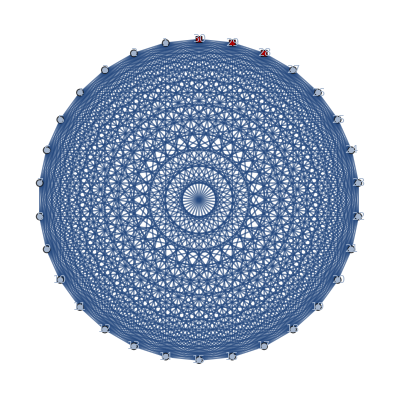

```mathematica
graph=CompleteGraph[numberOfEvents+numberOfGates,
VertexShapeFunction->verticesGatesShape,
VertexSize->0.2,
VertexStyle->verticesGatesColor,
VertexLabels->Placed["Name",Center]]
```

```mathematica
edgeList=DeleteDuplicates[SortBy[List@@@EdgeList[graph],First]];
```

```mathematica
vertexList=VertexList[graph];
```

```mathematica
alpha1=10;
alpha2=20;
alpha3=30;
```

### Определения предка события

```mathematica
successorsPairs=Flatten[Partition[#,2,1]&/@events,1]
```

{{1,2},{3,4},{4,5},{6,7},{7,8},{9,10},{10,11},{12,13},{14,15},{15,16},{17,18},{18,19},{20,21},{21,22},{23,24},{25,26},{26,27}}

```mathematica
Clear[u,event,successor]

Do[
{successor,event}=pair;
u[event]=successor,
{pair,successorsPairs}
]
```

### Определение веса

```mathematica
Clear[getWeightMatrix]
getWeightMatrix[{vertexList_:vertexList,edgeList_:edgeList},
			u_:u,
			{tmin_:tmin,numberOfEvents_:numberOfEvents,distanceMatrix_:distanceMatrix,preferences_:preferences},
			{alpha1_:alpha1,alpha2_:alpha2,alpha3_:alpha3}]:=Module[
{
weightMatrix=SparseArray[{{i_,j_}:>0},{Length[vertexList],Length[vertexList]}],
i,j
},
Do[
{i,j}=edge;
If[
i<=numberOfEvents∧j<=numberOfEvents,
If[
distanceMatrix⟦i,j⟧<0,
weightMatrix⟦i,j⟧=-∞,
If[
distanceMatrix⟦i,j⟧>=0∧(u[i]===j∨u[j]===i),
weightMatrix⟦i,j⟧=alpha2,
If[
distanceMatrix⟦i,j⟧>=0∧u[i]=!=u[j]∧u[j]=!=u[i],
weightMatrix⟦i,j⟧=alpha3*Max[tmin-distanceMatrix⟦i,j⟧,0]
]
]
],
If[
i<=numberOfEvents∧j>numberOfEvents,
If[
preferences⟦i,j-numberOfEvents⟧==-∞,
weightMatrix⟦i,j⟧=-∞,
weightMatrix⟦i,j⟧=alpha1*preferences⟦i,j-numberOfEvents⟧
],
weightMatrix⟦i,j⟧=-∞
]
],
{edge,edgeList}
];
weightMatrix
]
```

```mathematica
weightMatrix=getWeightMatrix[{vertexList,edgeList},u,{tmin,numberOfEvents,distanceMatrix,preferences},{alpha1,alpha2,alpha3}];
```

```mathematica
fullWeightMatrix=#+#ᵀ&@UpperTriangularize[weightMatrix];
```

### Целевая функция

```mathematica
Clear[targetFunction]
targetFunction[solution_,weightMatrix_]:=Module[
{
cliqueEdges=Partition[#,2,1,1]&/@solution
},
Total[Apply[fullWeightMatrix⟦##⟧&,cliqueEdges,{2}],2]
]
```

### Детерминированное начальное разбиение

```mathematica
Clear[h]
h[i_,C_,D_]:=Subtract@@Composition[Total,Map[fullWeightMatrix⟦i,#⟧&,#]&]/@{D,Complement[C,{i}]}
```

```mathematica
Clear[getAssignmentData]
getAssignmentData[clique_,nontabu_,u_,h_]:=Module[
{
currentSum,currentC,prevC,prevPrevC,
maxSum=-∞,maxVertex=0,maxD={}
},
Do[
currentC=clique⟦FirstPosition[clique,i]⟦1⟧⟧;
prevC=clique⟦FirstPosition[clique,u[i]]⟦1⟧⟧;
prevPrevC=clique⟦FirstPosition[clique,u[u[i]]]⟦1⟧⟧;
currentSum=h[i,currentC,D]+h[u[i],prevC,D]+h[u[u[i]],prevPrevC,D];
If[
currentSum>maxSum,
maxSum=currentSum;
maxVertex=i;
maxD=D;
],
{i,nontabu},
{D,clique}
];
{maxSum,maxVertex,maxD}
]
```

```mathematica
Clear[initialSolution]
initialSolution[vertexList_,u_,h_]:=Module[
{
clique=Partition[vertexList,1,1],
mask=Thread[And[Composition[NumberQ,u,u]/@vertexList,Composition[NumberQ,u]/@vertexList]],
tabu,nontabu,
maxSum,maxVertex,maxD,maxVertices,value
},
nontabu=Pick[vertexList,mask];
tabu=Complement[vertexList,nontabu];
While[
nontabu=!={},
{maxSum,maxVertex,maxD}=getAssignmentData[clique,nontabu,u,h];
If[
maxSum>0,
{maxSum,maxVertex,maxD}=getAssignmentData[clique,nontabu,u,h];
maxVertices={maxVertex,u[maxVertex],u[u[maxVertex]]};
value=DeleteDuplicates[clique⟦FirstPosition[clique,maxD]⟦1⟧⟧~Join~maxVertices];
clique⟦FirstPosition[clique,maxD]⟦1⟧⟧=value;
clique=DeleteCases[#,x_/;AnyTrue[value,x==#&]]&/@Complement[clique,value];
AppendTo[clique,value];
];
nontabu=DeleteCases[nontabu,maxVertex];
AppendTo[tabu,maxVertex];
];
DeleteCases[Sort/@clique,{}]
]
```

```mathematica
feasibleSolution=initialSolution[vertexList,u,h]
targetFunction[feasibleSolution,fullWeightMatrix]
```

{{1},{13},{23},{24},{29},{17,18,19},{20,21,22},{2,6,7,8},{3,4,5,12},{9,10,11,28},{14,15,16,30},{25,26,27}}

990

### Случайное начальное разбиение

```mathematica
Clear[randomInitialSolution]
randomInitialSolution[vertexList_,maxNumberInPart_:10,weightMatrix_]:=Module[
{
vertexCount=Length[vertexList],
shuffle=RandomSample[vertexList],
random,
cliques={},
i=1
},
While[i<vertexCount,
random=RandomInteger[Quotient[vertexCount,maxNumberInPart]];
If[i+random<vertexCount,
AppendTo[cliques,shuffle⟦i;;i+random⟧];
i+=random+1,
AppendTo[cliques,shuffle⟦i;;vertexCount⟧];
i=vertexCount]
];
If[Length[Flatten[cliques]]!=vertexCount∨targetFunction[cliques,weightMatrix]==-∞,
randomInitialSolution[vertexList,maxNumberInPart,weightMatrix],
cliques]
]
```

```mathematica
randomSolution=randomInitialSolution[vertexList,fullWeightMatrix]
```

{{21},{1,9},{13,2,22,16},{3,5,29},{8,19},{28,18,10},{23,30,7,11},{6,17},{26,15,4},{12,14},{25},{20,27,24}}

### Сравнение начальных разбиений (самоутверждение)

```mathematica
feasibleTFValue=targetFunction[feasibleSolution,fullWeightMatrix];
randomTFValue=targetFunction[randomSolution,fullWeightMatrix];

Style[
Grid[
{{"Название","Значение ЦФ"},
{"Детерминированное НР",feasibleTFValue},
{"Случайное НР",randomTFValue},
Style[#,Red]&/@{"∆",feasibleTFValue-randomTFValue}},
Frame->All,
Background->{None,{LightPurple}}],
FontSize->16,FontFamily->"Times New Roman"]
```

Название | Значение ЦФ
Детерминированное НР | 990
Случайное НР | 830
∆ | 160

### Алгоритм локального поиска

```mathematica
Clear[localSearch]
localSearch[solution_,numberOfIterations_,vertexList_,weightMatrix_]:=Module[
{
currentSolution=solution,
candidateSolution,
cliqueVariants,withoutVertex,selectedVertex,
cliquesTargetFunctionValue,
maxElementPosition,maxTargetFunctionValue
},
Do[
selectedVertex=RandomChoice[vertexList];
cliqueVariants=Table[
withoutVertex=Append[DeleteCases[currentSolution,selectedVertex,{2}],{}];
AppendTo[withoutVertex⟦i⟧,selectedVertex];
withoutVertex,
{i,Length[currentSolution]+1}];
cliquesTargetFunctionValue=targetFunction[#,weightMatrix]&/@cliqueVariants;
maxTargetFunctionValue=Max[cliquesTargetFunctionValue];
If[maxTargetFunctionValue!=-∞,
maxElementPosition=FirstPosition[cliquesTargetFunctionValue,Max[maxTargetFunctionValue]]⟦1⟧;
candidateSolution=DeleteCases[cliqueVariants⟦maxElementPosition⟧,{}];
If[maxTargetFunctionValue>targetFunction[currentSolution,weightMatrix],
currentSolution=candidateSolution],
Continue[]],
numberOfIterations];
currentSolution
]
```

```mathematica
localSearchSolution=localSearch[feasibleSolution,1000,vertexList,fullWeightMatrix]
targetFunction[localSearchSolution,fullWeightMatrix]
```

{{13,22},{23,30,16,15},{5,8},{17,18,19},{20,21},{2,6,7,24},{4,26},{9,10,11,28,12,3,1},{14,29},{25,27}}

1800

### Алгоритм имитации отжига

Функции изменения температуры

```mathematica
Clear[logarithmicSchedule]
Options[logarithmicSchedule]={CoolingSpeed->1.(*>=1*)};
logarithmicSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(OptionValue[CoolingSpeed] Log[iteration+1]+1)
```

```mathematica
Clear[geometricSchedule]
Options[geometricSchedule]={CoolingSpeed->0.85(*[0.8,0.9]*)};
geometricSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=OptionValue[CoolingSpeed]^iteration temp
```

```mathematica
Clear[linearSchedule]
Options[linearSchedule]={CoolingSpeed->0.85(*>0*)};
linearSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(1+OptionValue[CoolingSpeed] iteration)
```

```mathematica
Clear[quadraticSchedule]
Options[quadraticSchedule]={CoolingSpeed->0.85(*>0*)};
quadraticSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(1+OptionValue[CoolingSpeed] iteration^2)
```

```mathematica
Clear[getCandidate]
getCandidate[currentSolution_,selectedVertex_,weightMatrix_]:=Module[
{
cliqueVariants,
withoutVertex,
candidateSolution
},
While[True,
cliqueVariants=Table[
withoutVertex=Append[DeleteCases[currentSolution,selectedVertex,{2}],{}];
AppendTo[withoutVertex⟦i⟧,selectedVertex];
withoutVertex,
{i,Length[currentSolution]+1}];
If[AllTrue[targetFunction[#,weightMatrix]&/@cliqueVariants,#==-∞&],
Print["Stop by wrong vertex"];
Break[]];
candidateSolution=DeleteCases[RandomChoice[cliqueVariants],{}];
If[targetFunction[candidateSolution,weightMatrix]!=-∞,Break[]];
];
candidateSolution
]
```

```mathematica
Clear[simulatedAnnealing]
simulatedAnnealing[solution_,{tMin_,tMax_,temperatureFunction_,coolingSpeed_},vertexList_,weightMatrix_]:=Module[
{
tCurrent=tMax,
currentSolution=solution,
selectedVertex,withoutVertex,cliqueVariants,candidateSolution,
differenceTargetFunctions,i=1
},
While[tCurrent>tMin,
selectedVertex=RandomChoice[vertexList];
candidateSolution=getCandidate[currentSolution,selectedVertex,weightMatrix];
differenceTargetFunctions=targetFunction[candidateSolution,weightMatrix]-targetFunction[currentSolution,weightMatrix];
If[differenceTargetFunctions>0,
currentSolution=candidateSolution,
If[RandomReal[]<Exp[differenceTargetFunctions/tCurrent],
currentSolution=candidateSolution]
];
tCurrent=temperatureFunction[tCurrent,i,CoolingSpeed->coolingSpeed];
i+=1;
];
currentSolution
]
```

```mathematica
feasibleSolution
targetFunction[feasibleSolution,fullWeightMatrix]
```

{{1},{13},{23},{24},{29},{17,18,19},{20,21,22},{2,6,7,8},{3,4,5,12},{9,10,11,28},{14,15,16,30},{25,26,27}}

990

```mathematica
simulatedAnnealingSolution=Quiet@simulatedAnnealing[feasibleSolution,{0.01,150,logarithmicSchedule,1.5},vertexList,fullWeightMatrix]
targetFunction[simulatedAnnealingSolution,fullWeightMatrix]
```

Stop by wrong vertex

{{21,1},{13,22},{23},{29},{17,18,19},{20},{2,6,7,8},{3,4,5,12},{9,10,28,11},{14,15,16,30,24},{25,26,27}}

1060

### Алгоритм поиска с запретом

```mathematica
Clear[getCandidateList]
getCandidateList[currentSolution_,vertexList_]:=Module[
{
withoutVertex
},
Table[
Table[
withoutVertex=Append[DeleteCases[currentSolution,v,{2}],{}];
AppendTo[withoutVertex⟦i⟧,v];
DeleteCases[withoutVertex,{}],
{i,Length[currentSolution]+1}],
{v,vertexList}]
]
```

```mathematica
Clear[getDifferenceMatrix]
getDifferenceMatrix[currentSolution_,candidateList_,weightMatrix_]:=Map[targetFunction[#,weightMatrix]-targetFunction[currentSolution,weightMatrix]&,candidateList,{2}]
```

```mathematica
Clear[tabuSearch]
tabuSearch[solution_,numberOfIterations_,lenTS_,vertexList_,weightMatrix_]:=Module[
{
currentSolution=solution,
candidateList,candidateSolution,
M,
vertex,clique,
tabu={},
i=1
},
While[i<numberOfIterations∧Length[tabu]<lenTS,
candidateList=getCandidateList[currentSolution,vertexList];
M=getDifferenceMatrix[currentSolution,candidateList,weightMatrix];
If[Max[M]<0,
Print["Stop by negative difference"];
Break[],
{vertex,clique}=FirstPosition[M,Max[M]]
];
candidateSolution=candidateList⟦vertex,clique⟧;
While[candidateList!={}∧MemberQ[candidateSolution,tabu],
Print["Go in"];
candidateList=DeleteCases[candidateList,candidateSolution,{2}];
M=getDifferenceMatrix[currentSolution,candidateList,weightMatrix];
If[Max[M]<=0,
Print["Stop by nonpositive difference"];
Break[],
{vertex,clique}=FirstPosition[M,Max[M]]
];
candidateSolution=candidateList⟦vertex,clique⟧;
If[candidateList=={}∨!MemberQ[candidateSolution,tabu],Break[]]
];
currentSolution=candidateSolution;
AppendTo[tabu,candidateSolution]
];
currentSolution
]
```

```mathematica
tabuSearchSolution=tabuSearch[feasibleSolution,30,10,vertexList,fullWeightMatrix]
```

{{16,1},{13,22},{23,15},{24,2},{29,9},{17,18,19,14},{20,21},{6,7},{3,4,5,12},{10,11,28},{30,8},{25,26,27}}

```mathematica
targetFunction[tabuSearchSolution,fullWeightMatrix]
targetFunction[feasibleSolution,fullWeightMatrix]
```

1760

990

### Подбор гиперпараметров

#### GridSearch

```mathematica
Clear[GridSearch]
Options[GridSearch]={OneParameterIteration->1};
GridSearch[function_Symbol,args_List,parameters_Association,fullWeightMatrix_,OptionsPattern[]]:=Module[
{
parameterNames=Keys[parameters],
parameterValues=Values[parameters],
parametersList,
currentParamsValue,
bestParamsValue=-∞,bestParams
},
parametersList=Thread[parameterNames->#]&/@DeleteDuplicates[Flatten[Outer[List,Sequence@@parameterValues],2]];
Do[
currentParamsValue=Mean[Table[targetFunction[function[Sequence@@args,Sequence@@params],fullWeightMatrix],OptionValue[OneParameterIteration]]];
If[
currentParamsValue>bestParamsValue,
bestParamsValue=currentParamsValue;
bestParams=params
],
{params,parametersList}
];
{bestParams,N[bestParamsValue]}
]
```

#### Алгоритм имитации отжига

```mathematica
Clear[simulatedAnnealingGridSearch]
Options[simulatedAnnealingGridSearch]={tMin->0.5,tMax->10,CoolingSpeed->1};
simulatedAnnealingGridSearch[solution_,temperatureFunction_,vertexList_,weightMatrix_,OptionsPattern[]]:=simulatedAnnealing[solution,{OptionValue[tMin],OptionValue[tMax],temperatureFunction,OptionValue[CoolingSpeed]},vertexList,weightMatrix]
```

```mathematica
simulatedAnnealingParameters=Association[{"tMin"->{0.01,0.1,0.5},"tMax"->{10,50,100,200},"CoolingSpeed"->{1,1.5,2,3}}]
```

<|tMin→{0.01,0.1,0.5},tMax→{10,50,100,200},CoolingSpeed→{1,1.5,2,3}|>

```mathematica
Quiet@GridSearch[
simulatedAnnealingGridSearch,
{feasibleSolution,logarithmicSchedule,vertexList,fullWeightMatrix},
simulatedAnnealingParameters,
fullWeightMatrix,
OneParameterIteration->20]
```

Stop by wrong vertex

Stop by wrong vertex

Stop by wrong vertex

«1 more identical outputs»

{{tMin→0.01,tMax→100,CoolingSpeed→1.5},1188.}

#### Алгоритм поиска с запретом

```mathematica
Clear[tabuSearchGridSearch]
Options[tabuSearchGridSearch]={Iterations->30,MaxLengthTS->10};
tabuSearchGridSearch[solution_,vertexList_,weightMatrix_,OptionsPattern[]]:=tabuSearch[solution,OptionValue[Iterations],OptionValue[MaxLengthTS],vertexList,weightMatrix]
```

```mathematica
tabuSearchParameters=Association[{"Iterations"->{10,25,50,100},"MaxLengthTS"->{5,10,20,30}}]
```

<|Iterations→{10,25,50,100},MaxLengthTS→{5,10,20,30}|>

```mathematica
Quiet@GridSearch[
tabuSearchGridSearch,
{feasibleSolution,vertexList,fullWeightMatrix},
tabuSearchParameters,
fullWeightMatrix,
OneParameterIteration->1]
```

{{Iterations→10,MaxLengthTS→10},1760.}

### Сравнение и визуализация алгоритмов

```mathematica
Style[
Grid[
{{"Название","Значение ЦФ"},
{"Начальное решение",targetFunction[feasibleSolution,fullWeightMatrix]},
{"Локальный поиск",targetFunction[localSearchSolution,fullWeightMatrix]},
{"Имитация отжига",targetFunction[simulatedAnnealingSolution,fullWeightMatrix]},
{"Поиск с запретами",targetFunction[tabuSearchSolution,fullWeightMatrix]}},
Frame->All,
Background->{None,{LightPurple}}],
FontSize->16,FontFamily->"Times New Roman"]
```

Название | Значение ЦФ
Начальное решение | 990
Локальный поиск | 1800
Имитация отжига | 1060
Поиск с запретами | 1760

```mathematica
solutions={localSearchSolution,simulatedAnnealingSolution,tabuSearchSolution};
colors=RandomColor[Length[#]]&/@solutions;
edgesSolutions=Map[Partition[#,2,1,1]&,solutions,{2}];
edgesSolutionsColors=MapIndexed[UndirectedEdge@@#1->{colors⟦Sequence@@(#2⟦1;;2⟧)⟧,Thickness[0.01],Opacity[1]}&,edgesSolutions,{3}];

Panel[Manipulate[
Show[CompleteGraph[numberOfEvents+numberOfGates,
VertexShapeFunction->verticesGatesShape,
VertexSize->0.5,
VertexStyle->verticesGatesColor,
EdgeStyle->{Opacity[showEdges],Sequence@@Flatten[edgesSolutionsColors⟦algorithm⟧]},
VertexLabels->Placed["Name",Center]],ImageSize->Large],
Row[{Control[{{algorithm,1,"Алгоритм: "},{1->"Локальный поиск",2->"Имитация отжига",3->"Поиск с запретами"},RadioButton}]}],
Row[{Control[{{showEdges,1,"Рёбра: "},{0,1}}]}],
Paneled->False],
Style["Визуализация решений",20,Bold,FontFamily->"Times New Roman"]]
```

Визуализация решений